Run Td_realspace_rot.nb first

## Generate test data

```mathematica
(* j=3/2, l=1 basis states for the Subscript[Γ, 8] representation of the Subscript[T, d] double group *)
ψ32[x_,y_,z_]:={x+I y,0}/Sqrt[2];
ψ12[x_,y_,z_]:={-Sqrt[2/3]z,(x+I y)/Sqrt[6]};
ψm12[x_,y_,z_]:={-(x-I y)/Sqrt[6],-z Sqrt[2/3]};
ψm32[x_,y_,z_]:={0,-(x-I y)/Sqrt[2]};
(* build normalized test data *)
test[x_,y_,z_]:=ψ12[x,y,z];
NN=NIntegrate[test[x,y,z]*.test[x,y,z],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}]
Test[x_,y_,z_]:=1/(√NN)test[x,y,z]
(*Check normalization*)
NIntegrate[Test[x,y,z]*.Test[x,y,z],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}]

Δ=11; (*step size for discretization of Test*)

(*Generate test data*)
T=Flatten[Table[{{x,y,z},Test[x,y,z]},{x,-0.5,0.5,Δ^-1},{y,-0.5,0.5,Δ^-1},{z,-0.5,0.5,Δ^-1}],2];
```

0.0833333

1.

### Plot test data

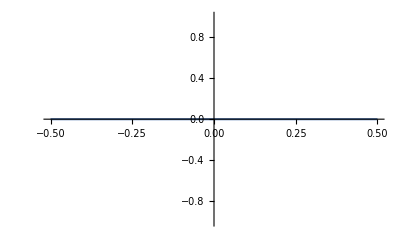
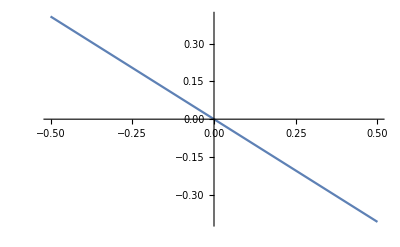
{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[test[x,0,0][[1]]],{x,-0.5,0.5},PlotRange->All],Plot[Re[test[0,x,0][[1]]],{x,-0.5,0.5},PlotRange->All], Plot[Re[test[0,0,x][[1]]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[test[x,0,0][[1]]],{x,-0.5,0.5},PlotRange->All],Plot[Im[test[0,x,0][[1]]],{x,-0.5,0.5},PlotRange->All], Plot[Im[test[0,0,x][[1]]],{x,-0.5,0.5},PlotRange->All]}
```

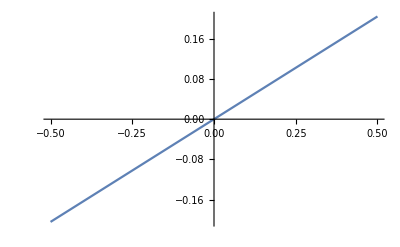
{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[test[x,0,0][[2]]],{x,-0.5,0.5},PlotRange->All],Plot[Re[test[0,x,0][[2]]],{x,-0.5,0.5},PlotRange->All], Plot[Re[test[0,0,x][[2]]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[test[x,0,0][[2]]],{x,-0.5,0.5},PlotRange->All],Plot[Im[test[0,x,0][[2]]],{x,-0.5,0.5},PlotRange->All], Plot[Im[test[0,0,x][[2]]],{x,-0.5,0.5},PlotRange->All]}
```

## Projections

```mathematica
h=4; (* dimensonality of the representaton *)
L=48; (* number of elements in the group *)

UP=Table[{T[[ii,1]],T[[ii,2,1]]},{ii,1,Length[T]}];
DOWN=Table[{T[[ii,1]],T[[ii,2,2]]},{ii,1,Length[T]}];

state[r_]:={Interpolation[UP][r[[1]],r[[2]],r[[3]]],Interpolation[DOWN][r[[1]],r[[2]],r[[3]]]}

rstate[n_,r_]:=rs[n].state[Rm[n].{r[[1]],r[[2]],r[[3]]}]
Proj[ii_,jj_,r_]:=h/L*Sum[Ρ[n][[ii,jj]]**rstate[n,r],{n,1,L}]
```

Plots 1/2-> 1/2

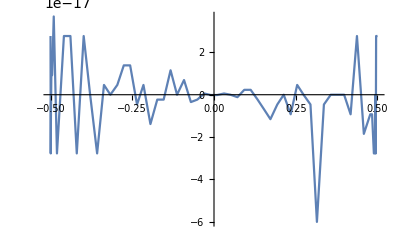
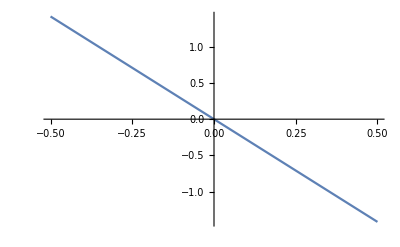
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[Proj[3,3,{x,0,0}]][[1]],{x,-0.5,0.5},PlotRange->All],Plot[Re[Proj[3,3,{0,x,0}]][[1]],{x,-0.5,0.5},PlotRange->All], Plot[Re[Proj[3,3,{0,0,x}]][[1]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[Proj[3,3,{x,0,0}]][[1]],{x,-0.5,0.5},PlotRange->All],Plot[Im[Proj[3,3,{0,x,0}]][[1]],{x,-0.5,0.5},PlotRange->All], Plot[Im[Proj[3,3,{0,0,x}]][[1]],{x,-0.5,0.5},PlotRange->All]}
```

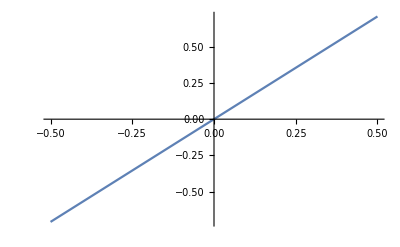
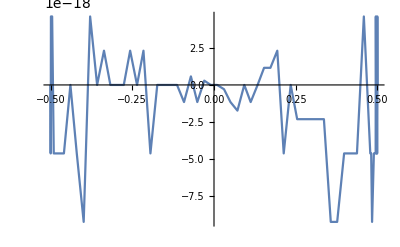
{-Graphics-,-Graphics-,-Graphics-}

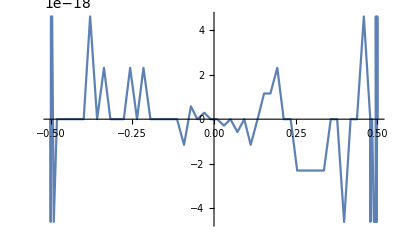
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[Proj[3,3,{x,0,0}]][[2]],{x,-0.5,0.5},PlotRange->All],Plot[Re[Proj[3,3,{0,x,0}]][[2]],{x,-0.5,0.5},PlotRange->All], Plot[Re[Proj[3,3,{0,0,x}]][[2]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[Proj[3,3,{x,0,0}]][[2]],{x,-0.5,0.5},PlotRange->All],Plot[Im[Proj[3,3,{0,x,0}]][[2]],{x,-0.5,0.5},PlotRange->All], Plot[Im[Proj[3,3,{0,0,x}]][[2]],{x,-0.5,0.5},PlotRange->All]}
```

## Plots -3/2 ->-3/2

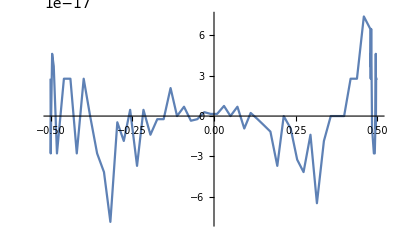
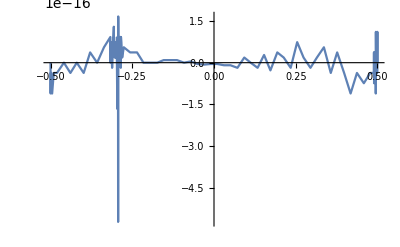
{-Graphics-,-Graphics-,-Graphics-}

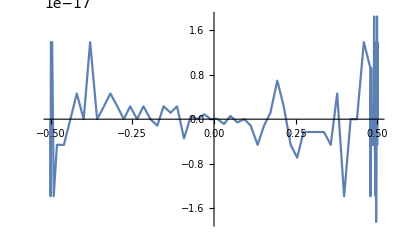
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[Proj[1,1,{x,0,0}]][[1]],{x,-0.5,0.5},PlotRange->All],Plot[Re[Proj[1,1,{0,x,0}]][[1]],{x,-0.5,0.5},PlotRange->All], Plot[Re[Proj[1,1,{0,0,x}]][[1]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[Proj[1,1,{x,0,0}]][[1]],{x,-0.5,0.5},PlotRange->All],Plot[Im[Proj[1,1,{0,x,0}]][[1]],{x,-0.5,0.5},PlotRange->All], Plot[Im[Proj[1,1,{0,0,x}]][[1]],{x,-0.5,0.5},PlotRange->All]}
```

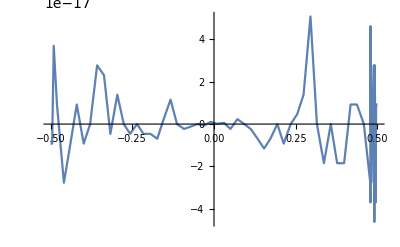
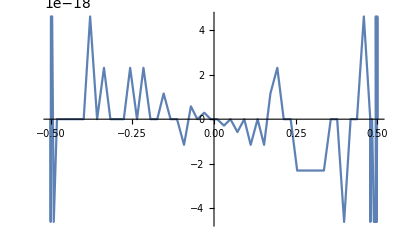
{-Graphics-,-Graphics-,-Graphics-}

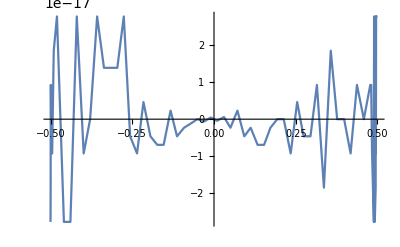
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[Proj[1,1,{x,0,0}]][[2]],{x,-0.5,0.5},PlotRange->All],Plot[Re[Proj[1,1,{0,x,0}]][[2]],{x,-0.5,0.5},PlotRange->All], Plot[Re[Proj[1,1,{0,0,x}]][[2]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[Proj[1,1,{x,0,0}]][[2]],{x,-0.5,0.5},PlotRange->All],Plot[Im[Proj[1,1,{0,x,0}]][[2]],{x,-0.5,0.5},PlotRange->All], Plot[Im[Proj[1,1,{0,0,x}]][[2]],{x,-0.5,0.5},PlotRange->All]}
```

## Plots 1/2 ->-3/2

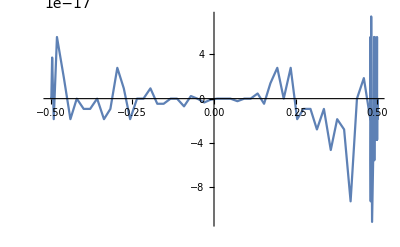
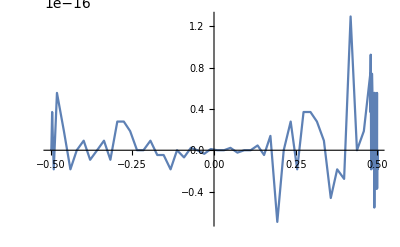
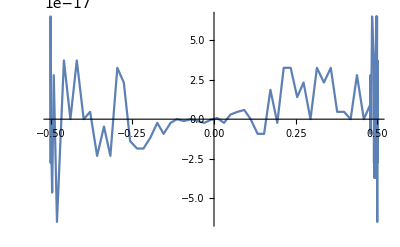

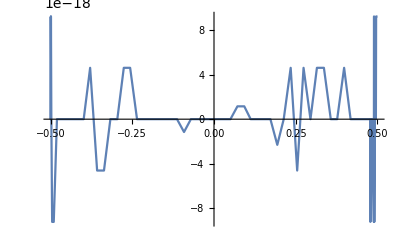
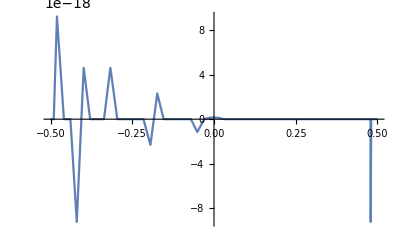
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[Proj[1,3,{x,0,0}]][[1]],{x,-0.5,0.5},PlotRange->All],Plot[Re[Proj[1,3,{0,x,0}]][[1]],{x,-0.5,0.5},PlotRange->All], Plot[Re[Proj[1,3,{0,0,x}]][[1]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[Proj[1,3,{x,0,0}]][[1]],{x,-0.5,0.5},PlotRange->All],Plot[Im[Proj[1,3,{0,x,0}]][[1]],{x,-0.5,0.5},PlotRange->All], Plot[Im[Proj[1,3,{0,0,x}]][[1]],{x,-0.5,0.5},PlotRange->All]}
```

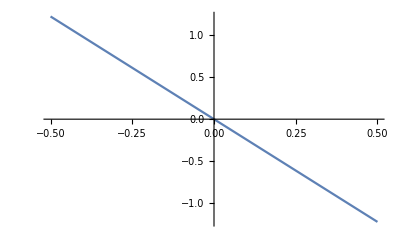
{-Graphics-,-Graphics-,-Graphics-}

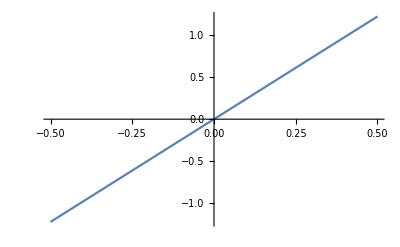
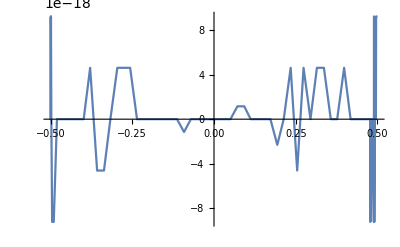
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[Proj[1,3,{x,0,0}]][[2]],{x,-0.5,0.5},PlotRange->All],Plot[Re[Proj[1,3,{0,x,0}]][[2]],{x,-0.5,0.5},PlotRange->All], Plot[Re[Proj[1,3,{0,0,x}]][[2]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[Proj[1,3,{x,0,0}]][[2]],{x,-0.5,0.5},PlotRange->All],Plot[Im[Proj[1,3,{0,x,0}]][[2]],{x,-0.5,0.5},PlotRange->All], Plot[Im[Proj[1,3,{0,0,x}]][[2]],{x,-0.5,0.5},PlotRange->All]}
```

## Discrete Test

```mathematica
m1=3;
m2=3;

ROTtab=Table[Sort[Table[{R[ii].T[[jj,1]],Conjugate[Ρ[ii][[m1,m2]]]*rs[ii].T[[jj,2]]},{jj,1,Length[T]}]],{ii,1,L}];
Ftab=Table[{ROTtab[[1,ii,1]],h/L*Sum[ROTtab[[n,ii,2]],{n,1,L}]},{ii,1,Length[T]}];
```

```mathematica
v=Interpolation[Ftab]
view[x_,y_,z_]:=v[x,y,z]
```

InterpolatingFunction[{{-0.5, 0.5}, {-0.5, 0.5}, {-0.5, 0.5}}, <>]

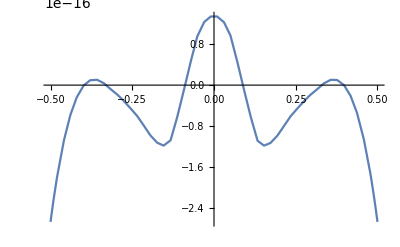
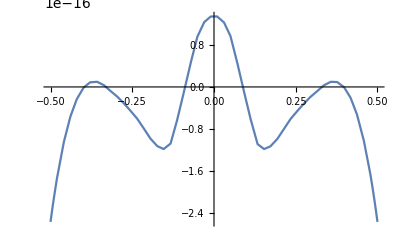
{-Graphics-,-Graphics-,-Graphics-}

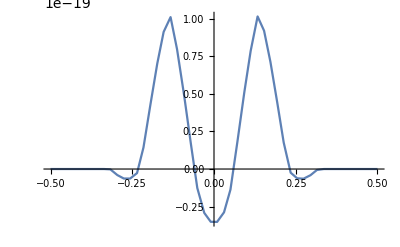
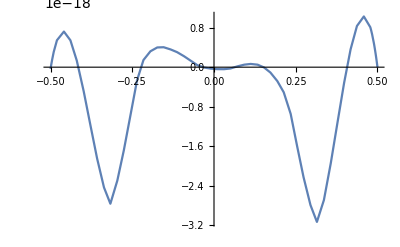
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[view[x,0,0][[1]]],{x,-0.5,0.5},PlotRange->All],Plot[Re[view[0,x,0][[1]]],{x,-0.5,0.5},PlotRange->All], Plot[Re[view[0,0,x][[1]]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[view[x,0,0][[1]]],{x,-0.5,0.5},PlotRange->All],Plot[Im[view[0,x,0][[1]]],{x,-0.5,0.5},PlotRange->All], Plot[Im[view[0,0,x][[1]]],{x,-0.5,0.5},PlotRange->All]}
```

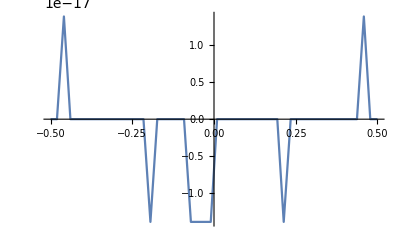
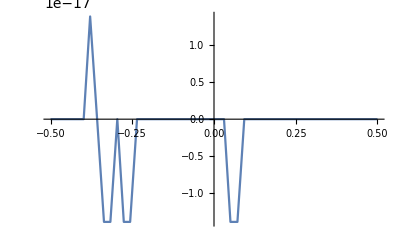
{-Graphics-,-Graphics-,-Graphics-}

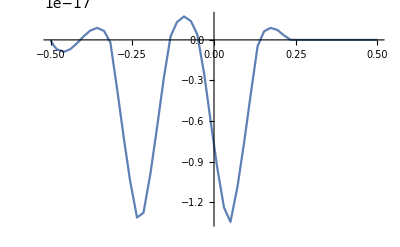
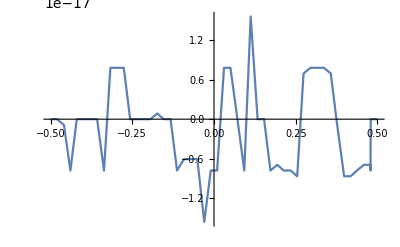
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[Re[view[x,0,0][[2]]],{x,-0.5,0.5},PlotRange->All],Plot[Re[view[0,x,0][[2]]],{x,-0.5,0.5},PlotRange->All], Plot[Re[view[0,0,x][[2]]],{x,-0.5,0.5},PlotRange->All]}
{Plot[Im[view[x,0,0][[2]]],{x,-0.5,0.5},PlotRange->All],Plot[Im[view[0,x,0][[2]]],{x,-0.5,0.5},PlotRange->All], Plot[Im[view[0,0,x][[2]]],{x,-0.5,0.5},PlotRange->All]}
```

### Normalization Check

```mathematica
Sum[T[[i,2]]*.T[[i,2]],{i,1,Length[T]}]*(Δ)^3
```

1.53432+0. ⅈ

```mathematica
Sum[Ftab[[i,2]]*.Ftab[[i,2]],{i,1,Length[T]}]*(Δ)^3
```

1.53432+0. ⅈ